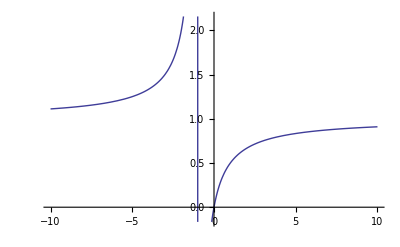

```mathematica
Plot[x/(1+x),{x,-10,10}]
```

```mathematica
(*piecewise linear function for Si vs Se*)
Plot[Piecewise[{{0,}  }]   ]
```

```mathematica
Io=3/20;
```

```mathematica
(*2nd test for piecewise linear, with ke and ki, without boundary conditions*)
For[Jii=0.001,Jii≤.1,Jii=Jii+.001,For[Jie=0.01,Jie≤1,Jie=Jie+.04,For[Jee=0.1,Jee≤1,Jee=Jee+.04,
c1=a (ce(Is+Io)-eIth);c2=a ce Jee; c3=a ce Jie;c4= ci Io-iIth;c5=ci Jei;c6=ci Jii;c9=-k1 c3 k2 c2/(1/ti+k2 c6)-k1 c2;c10=k1 c2 -1/te -k1 c1 -(c4+c2)k1 c3 k2 /(1/ti +k2 c6); c11=k1 c1-k1 c3 k2 c4/(1/ti +k2 c6); Se=(-c10-Sqrt[c10 ^2-4 c9 c11])/(2 c9);Si=k2(c4+c2 Se)/(1/ti + k2 c6);c7 = 1/te-k1 c2 +2 k1 c2 Se+1/ti +k2 c6;c8=1/(te ti)+k2 c6/(te)-k1 c2/ti -k1 c2 k2 c6 + 2 k1 c2 Se/ti+k1 k2 c5 c3+2 k2 c6 k1 c2 Se -k1 k2 c3 c5 Se;If[Re[c7]>-.5 && Re[c7]<.5 && Im[c8]==0&& Re[c8]>0&&Se>0&&Se<.9&&Si>0&&Si<1 && k2 c2/(1/ti + k2 c6) > (c2-1/(k1 (1-Se) te)-Se/(k1 (1-Se)^2 te))/c3,{Print["Io=",Io, " Jie=",Jie," Jii=",Jii," Jee=",Jee," Se=",Se," Si=",Si," Ie=",Jee Se-Jie Si +Is+Io," Ii=",Jei Se -Jii Si+Io] },Continue[]]  ]]]
```

```mathematica
.
```

```mathematica
Im[Se]==0&& Im[Si]==0&&
```

```mathematica
Re[c7]>-.5 && Re[c7]<.5 && Im[c8]==0&& Re[c8]>0&&
```